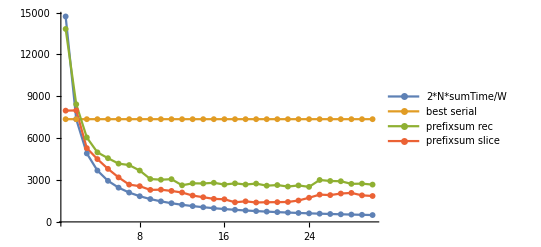

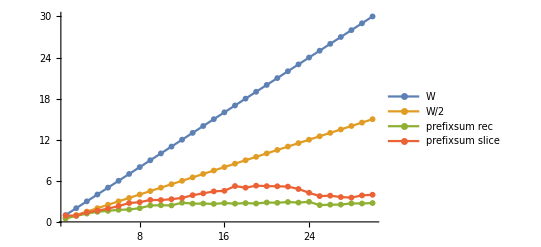

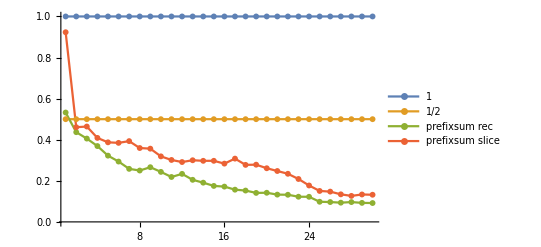

```mathematica
nameRec := "prefixsum rec"
nameSlice := "prefixsum slice" 
timesRec := {13829.73,8429.04,6050.94,4986.54,4566.11,4177.63,4073.30,3680.59,3073.52,3024.68,3061.54,2624.63,2764.97,2754.67,2803.13,2678.56,2761.19,2681.01,2745.30,2596.13,2639.82,2533.42,2612.90,2510.81,3004.67,2932.35,2914.36,2726.28,2742.36,2673.19}
timesSlice := {7974.93,7989.68,5286.74,4502.23,3801.44,3189.93,2675.09,2559.67,2294.62,2308.29,2220.13,2105.58,1887.61,1768.92,1650.80,1622.22,1406.18,1473.59,1391.35,1409.61,1415.44,1428.93,1532.81,1730.44,1955.46,1921.40,2032.66,2076.96,1902.44,1857.25}
best1 := 7362.85

idealTime[w_] := 2*best1/w
idealTimes := Map[idealTime, Range[30]]
ListLinePlot[{idealTimes, ConstantArray[best1, 30], timesRec, timesSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"2*N*sumTime/W", "best serial", nameRec, nameSlice}]

speedupFunc[x_] := best1/ x
speedupRec := Map[speedupFunc, timesRec]
speedupSlice := Map[speedupFunc, timesSlice]
ListLinePlot[{Range[30], Range[0.5, 15, 0.5], speedupRec, speedupSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"W", "W/2", nameRec, nameSlice}]

efficFuncRec[x_] := speedupRec[[x]]/ x
efficFuncSlice[x_] := speedupSlice[[x]]/ x
efficRec := Map[efficFuncRec, Range[30]]
efficSlice := Map[efficFuncSlice, Range[30]]
ListLinePlot[{ConstantArray[1, 30], ConstantArray[0.5, 30], efficRec, efficSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"1", "1/2", nameRec, nameSlice}]
```